```mathematica
Lab M1: The Simple Pendulum
```

```mathematica
Introduction to Part 1
	In the first part of this lab the goal was to determine the value of acceleration due to gravity. This would be determined by using a simple pendulum. Using the equations the center of mass can be calculated. Then the period can be found by swinging the mass throguh the photogate which then measures the period of mass. After we have both of the values, the acceleration of gravity can be found.
```

```mathematica
Part 1:Finding the acceleration due to gravity
```

```mathematica
h=0.03815; (*Height of the mass (m)*)
δh=0.00015; (*Uncertainity of the height of the mass (m)*)
λ=1.0225; (*Length of the string (m)*)
δλ=0.0025; (*Uncertainity of the length of the string*)
L=λ+(1/2*h); (*Length of the pendulum*)
δL=√((δλ)^2+(δh/2)^2); (*Calculated uncertainity of the length of the pendulum*)
T= {2.0499, 2.0480, 2.0417};
δT=(Abs[T[[1]]-T[[3]]])/2; (*Uncertainity in the period measurements (s)*)
```

```mathematica
Introduction to Part 2
	In this part, the relationship between the period and the length of the string would be graphed and analyzed. Both period and the length of each of the strings woul dbe measured and then the data would be used to compare the two.
```

```mathematica
Part 2:Dependence of Time on Length
```

{1.13408,0.821075,0.375075,0.642075,1.04158}

Length of Pendulum(m) | Period of Pendulum(s)
1.13408 | 2.148
0.821075 | 1.83
0.375075 | 1.239
0.642075 | 1.619
1.04158 | 2.045

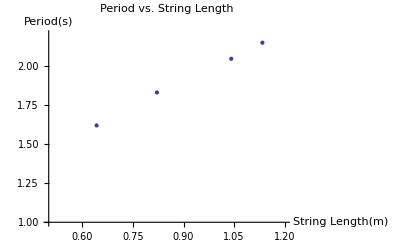

```mathematica
λ2={1.115, 0.802, 0.356, 0.623, 1.0225}; (*Lengths of all the strings used (m)*)
L2= λ2+h/2//N (*The total length from the top of the string to the center of mass(m)*)
T2= {2.148, 1.830, 1.239, 1.619, 2.045};(*The periods of each of the lengths (s)*)
δT2= 0.001; (*the uncertaintiy of the periods (s)*)
L2vsT2= Thread[{L2,T2}];
Grid[Prepend[L2vsT2,{"Length of Pendulum(m)","Period of Pendulum(s)"}], Frame->All]
ListPlot[{L2vsT2}, PlotLabel->"Period vs. String Length",AxesLabel->{"String Length(m)","Period(s)"}, PlotRange->{{.5,1.2},{1,2.2}}]
```

```mathematica
Introduction to Part 3
	In the final part of this lab we would realize how the period varies by a change of amplitude (degrees) of the wing. Different angles would be used from 5-70 with a 5 degree increase each time and then each time the period would be measured.
```

```mathematica
Part 3:Dependence of T on Amplitude
```

Amplitude (rad) | Period(s)
0.0872665 | 2.0469
0.174533 | 2.0498
0.261799 | 2.0563
0.349066 | 2.0627
0.436332 | 2.0717
0.523599 | 2.0834
0.610865 | 2.0931
0.698132 | 2.1068
0.785398 | 2.13
0.872665 | 2.145
0.959931 | 2.178
1.0472 | 2.1956
1.13446 | 2.225
1.22173 | 2.2362

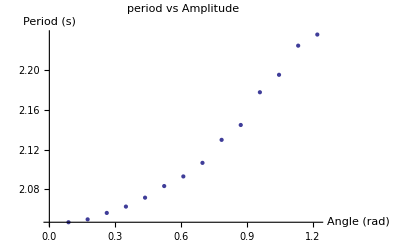

```mathematica
A={5,10,15,20,25,30,35,40,45,50,55,60,65,70}; (*Angles of initial height of pendulum (Degrees)*)
δA=0.5; (*Uncertainty of the initial angle (Degrees)*)
θ=A*(π/180)//N;(*Converting the uncertainty all the angles from degrees to radians*)
δθ=δA*(π/180);(*Converting the uncertainity from degrees to radians*)
T3={2.0469, 2.0498, 2.0563, 2.0627, 2.0717, 2.0834, 2.0931, 2.1068, 2.1300, 2.1450, 2.1780, 2.1956, 2.2250, 2.2362}; (*Period from each of the angles respectively*)
δT3=0.0001; (*Uncertainty of the period*)
T3vsθ=Thread[{θ, T3}];
Grid[Prepend[T3vsθ,{"Amplitude (rad)", "Period(s)"}], Frame->All]
ListPlot[{T3vsθ}, PlotLabel->"period vs Amplitude", AxesLabel->{"Angle (rad)", "Period (s)"}]
```

```mathematica
Data Analysis and Discussion
```

```mathematica
Part 1: Finding the acceleration due to gravity
```

```mathematica
Tmeasured=2.0480;(*The middle value of the three trials of the period is also refered to as the Best Fit (s)*)
gmeasured=4*π^2*(L/Tmeasured^2)(*calculated acceleration due to gravity from measurements of length and period(m/s^2)*)
δmeasured=gmeasured*√((δL/L)^2+(2*δT/Tmeasured)^2)(*Uncertainty in the measured acceleration due to gravitiy (m/s^2)*)
```

9.80371

0.0457713

```mathematica
The experimental g calculated was (9.80±0.046)(m/s^2). Using equation 12, the uncertainity of g was calculated.
```

```mathematica
gknown=9.796;
Δg=gmeasured-gknown (*finding the difference of the g's to see if the error falls within it*)
```

0.00770827

```mathematica
The difference between the measured g and the theoretical g is within the error bound, leading to the conclusion that the data is plausible.
```

```mathematica
Part 2: Dependence of Time on Length
```

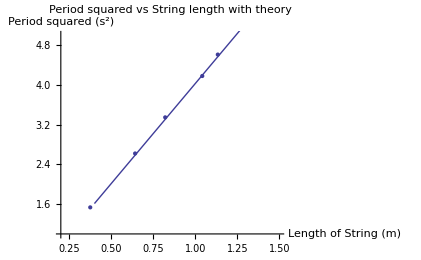

```mathematica
P=T2^2;(*Period Squared (s^2)*)
y[x_]=(4*π^2/9.796)*x;(*Equation for the theoretical dependence of period squared vs string length*)
PvsL2=Thread[{L2,P}];
PvsL2graph= ListPlot[PvsL2, PlotLabel->"Period squared vs String length with theory", AxesLabel->{"Length of String (m)", "Period squared (s^2)"}, PlotRange->{{0.2,1.5},{1,5}}];
PvsL2theory=Plot[y[x],{x,.4,2.0}];
Show[PvsL2graph,PvsL2theory]
```

```mathematica
When the period T is squared it forms a linear line, however, when its un-squared it creates a parabola. In simple words, having the period squared allows us to have a Best Fit Line for the graph and calculations.
```

```mathematica
Part 3: Dependence of T on amplitude
```

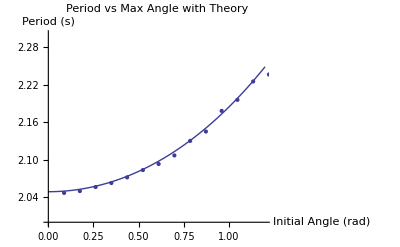

```mathematica
PA[ϕ_]=2*π*√(L/9.796)*(1+1/16 ϕ^2+11/3072 ϕ^4);(*Equation 11 (Theoretical)*)
PAgraph=ListPlot[T3vsθ, PlotLabel->"Period vs Max Angle with Theory",AxesLabel->{"Initial Angle (rad)","Period (s)"}, PlotRange-> {{0,1.2},{2,2.3}}];
PAtheory=Plot[PA[ϕ],{ϕ,0,1.2}];
Show[PAgraph, PAtheory]
```

```mathematica
Conclusions 

Part 1:Precision determination of g
	The experimental g was (9.80±0.0045)(m/s^2).This value is accepted because it lies in the error bound of the gravity of Boulder 9.796 (m/s^2).The amount of error can be explained to the lack of accuracy of the degrees measured from which the pendulum was released giving us a more accurate g than what was given during this lab experiment.
```

```mathematica
Part 2:Dependence of Time on Length 
	When the period was squared it results into a linear function (best fit line) allowing us to do more precise calculations based on the graph. The points fall close enough to the linear line giving us an idea of the error. The error is extremely small which is reflected by the linear graph. The error can be explained through the measurement of the strings with the 2 meter stick. The 2 meter stick was not accurate nor was it easy to spread out the string on the stick to get an exact measurement. The precision lies in millimeters which isnt as accurate. The data recorded is still precise but it could be more precise with a better and more accurate measuring tool.
```

```mathematica
Part 3: Dependence of time on amplitude 
	The data collected happens to accurate as it is pretty close to the theoretical line. There are few data points that are a little bit off, mostly the later ones because as the mass passes through more air resistance, it lowers the amplitude leading to shortening the amplitude. The more acurate angels were the lower ones in comparision to the higher ones.
```